Universal Quantum Computation: Demonstration |

Here we provide a simple demonstration that any arbitrary unitary operation can be implemented by combining CNOT gate and single-qubit rotations.

TwoLevelDecompositionpaclet:Q3/ref/TwoLevelDecompositionQ3 Package Symbol | Decomposes a unitary operator into a list of two-level unitary operators
TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol | Represents a two-level unitary operator
FromTwoLevelUpaclet:Q3/ref/FromTwoLevelUQ3 Package Symbol | Rewrites a two-level unitary operators in terms of CNOT and controlled-unitary gates

Some functions conveniently used for the demonstration of universal quantum computation.

### Step 1. Decomposition into two-Level unitary operations

We first decompose the unitary operation into two-level unitary operations, that is, unitary operators acting only on a two-dimensional subspace.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Consider a 2^n×2^n unitary matrix.

```mathematica
n=2;
mat=RandomUnitary[2^n];
mat//MatrixForm
```

(-0.0801213-0.384781 ⅈ | 0.392615+0.66088 ⅈ | 0.435636-0.116536 ⅈ | -0.0569277+0.219124 ⅈ
-0.353158-0.562473 ⅈ | 0.0187948-0.463124 ⅈ | 0.270516+0.442257 ⅈ | -0.246583-0.120386 ⅈ
0.458868-0.411535 ⅈ | -0.249473-0.320402 ⅈ | 0.269288-0.616527 ⅈ | 0.0499628+0.00818686 ⅈ
-0.156382-0.00713421 ⅈ | -0.0991722+0.139728 ⅈ | 0.27373+0.017924 ⅈ | 0.636079-0.682853 ⅈ)

This is an explicit operator expression of the unitary transformation.

```mathematica
nn=Range[n];
SS=S[nn,None];
opU=ExpressionFor[mat,SS]
```

(0.21101-0.536821 ⅈ)+(0.0669689+0.0030042 ⅈ) S_1^z S_2^z+(0.171326+0.326346 ⅈ) S_1^z S_2^+-(0.313444+0.290198 ⅈ) S_1^z S_2^-+(0.341109+0.00192492 ⅈ) S_1^+S_2^z-(0.0569277-0.219124 ⅈ) S_1^+S_2^++(0.270516+0.442257 ⅈ) S_1^+S_2^-+(0.27902-0.275632 ⅈ) S_1^-S_2^z-(0.249473+0.320402 ⅈ) S_1^-S_2^+-(0.156382+0.00713421 ⅈ) S_1^-S_2^--(0.241673-0.112869 ⅈ) S_1^z+(0.0945264-0.118461 ⅈ) S_1^++(0.179848-0.135903 ⅈ) S_1^--(0.116427-0.0361674 ⅈ) S_2^z+(0.221289+0.334533 ⅈ) S_2^+-(0.0397138+0.272274 ⅈ) S_2^-

Here is a two-level decomposition, where the results are in terms of TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol.

```mathematica
mm=TwoLevelDecomposition[mat]
```

{TwoLevelU[{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.961208+0.275825 ⅈ}},{3,4},4],TwoLevelU[{{0.721552-0.647123 ⅈ,0.23946+0.0570437 ⅈ},{-0.23946+0.0570437 ⅈ,0.721552+0.647123 ⅈ}},{3,4},4],TwoLevelU[{{0.384066+0.6117 ⅈ,0.691604},{-0.691604,0.384066-0.6117 ⅈ}},{2,3},4],TwoLevelU[{{-0.535991+0.827398 ⅈ,-0.0261928-0.16565 ⅈ},{0.0261928-0.16565 ⅈ,-0.535991-0.827398 ⅈ}},{3,4},4],TwoLevelU[{{-0.0801213-0.384781 ⅈ,0.919524},{-0.919524,-0.0801213+0.384781 ⅈ}},{1,2},4],TwoLevelU[{{0.426977+0.71872 ⅈ,0.548756},{-0.548756,0.426977-0.71872 ⅈ}},{2,3},4],TwoLevelU[{{0.863339-0.23095 ⅈ,-0.112819+0.434258 ⅈ},{0.112819+0.434258 ⅈ,0.863339+0.23095 ⅈ}},{3,4},4]}

You can convert the above results to more human readable full matrix form by means of Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

```mathematica
MatrixForm/@Matrix/@mm
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1.+0. ⅈ | 0
0 | 0 | 0 | 0.961208+0.275825 ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.721552-0.647123 ⅈ | 0.23946+0.0570437 ⅈ
0 | 0 | -0.23946+0.0570437 ⅈ | 0.721552+0.647123 ⅈ),(1 | 0 | 0 | 0
0 | 0.384066+0.6117 ⅈ | 0.691604 | 0
0 | -0.691604 | 0.384066-0.6117 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.535991+0.827398 ⅈ | -0.0261928-0.16565 ⅈ
0 | 0 | 0.0261928-0.16565 ⅈ | -0.535991-0.827398 ⅈ),(-0.0801213-0.384781 ⅈ | 0.919524 | 0 | 0
-0.919524 | -0.0801213+0.384781 ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0.426977+0.71872 ⅈ | 0.548756 | 0
0 | -0.548756 | 0.426977-0.71872 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.863339-0.23095 ⅈ | -0.112819+0.434258 ⅈ
0 | 0 | 0.112819+0.434258 ⅈ | 0.863339+0.23095 ⅈ)}

Check the decomposition with the original matrix.

```mathematica
new=Dot@@Matrix/@mm;
mat-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Step 2. Rewriting two-level unitary operators to elementary gates.

Now we rewrite each two-level unitary operator in terms of elementary gates, that is, in a combination of CNOT gates and one controlled-U gate.

FromTwoLevelUpaclet:Q3/ref/FromTwoLevelUQ3 Package Symbol does the job.

```mathematica
gates=Catenate[FromTwoLevelU[#,S@nn]&/@mm]
```

{ControlledU[{S_1},(0.980604+0.137913 ⅈ)+(0.0193961-0.137913 ⅈ) S_2^z,Label→U],ControlledU[{S_1},(0.721552+0. ⅈ)+(0.+0.0570437 ⅈ) S_2^x+(0.+0.23946 ⅈ) S_2^y-(0.+0.647123 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.384066+0. ⅈ)-(0.+0.691604 ⅈ) S_2^y-(0.+0.6117 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.535991+0. ⅈ)-(0.+0.16565 ⅈ) S_2^x-(0.+0.0261928 ⅈ) S_2^y+(0.+0.827398 ⅈ) S_2^z,Label→U],{S_1^x},ControlledU[{S_1},(-0.0801213+0. ⅈ)+(0.+0.919524 ⅈ) S_2^y-(0.+0.384781 ⅈ) S_2^z,Label→U],{S_1^x},CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.426977+0. ⅈ)-(0.+0.548756 ⅈ) S_2^y-(0.+0.71872 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.863339+0. ⅈ)+(0.+0.434258 ⅈ) S_2^x-(0.+0.112819 ⅈ) S_2^y-(0.+0.23095 ⅈ) S_2^z,Label→U]}

Here is a quantum circuit model of the decomposition. Here controlled-U gates are all labeled by the same character "U" but in fact they are different operators. Also do not forget to reverse the order of the elementary gates in the quantum circuit model.

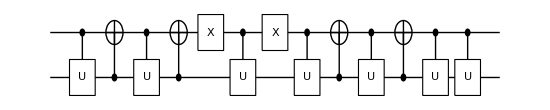

```mathematica
qc=QuantumCircuit[Sequence@@Reverse@gates]
```

```mathematica
new=ExpressionFor[qc]
```

(0.21101-0.536821 ⅈ)-(0.0480667-0.083461 ⅈ) S_1^x S_2^x+(0.1341-0.105134 ⅈ) S_1^x S_2^y+(0.310065-0.136854 ⅈ) S_1^x S_2^z-(0.247229-0.154861 ⅈ) S_1^y S_2^x+(0.0585883-0.0225338 ⅈ) S_1^y S_2^y-(0.138778-0.0310446 ⅈ) S_1^y S_2^z-(0.071059-0.018074 ⅈ) S_1^z S_2^x-(0.308272-0.242385 ⅈ) S_1^z S_2^y+(0.0669689+0.0030042 ⅈ) S_1^z S_2^z+(0.137187-0.127182 ⅈ) S_1^x-(0.00872132+0.0426607 ⅈ) S_1^y-(0.241673-0.112869 ⅈ) S_1^z+(0.0907876+0.0311294 ⅈ) S_2^x-(0.303404-0.130501 ⅈ) S_2^y-(0.116427-0.0361674 ⅈ) S_2^z

```mathematica
new-opU//Elaborate//Chop
```

0

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Systems with Q3
▪Universal Quantum Computation
▪QuantumCircuit Usage Examples
▪Quantum Fourier Transform
▪Quantum Teleportation

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/